# Plots Maximum Metric Across Signals for epoch

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
bcRateKHz = 28608.8064;
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Select which metric to plot.*)
availableMetrics = {"loss_bce", "score_rate0.3", "score_rate1"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection"}}])&
],availableMetrics]
desiredMetricPlotStyling = <|"loss_bce"->"BCE", "score_rate0.3"->"TPR @ 10^-5 FPR (probs.)"|>;
```

```mathematica
(*get the experiment dir and runs*)
experimentDir=FileNameJoin[{dataDir,experimentName}];
runDirs=FileNames[All,experimentDir];
runNames=FileNameTake/@runDirs;

pathsByRun=<||>;
desiredRuns={};

DynamicModule[
{},
Column[
{
Style["Select one or more runs:",Bold],
CheckboxBar[
Dynamic[desiredRuns,(
desiredRuns=#;
pathsByRun=Association@Table[runName->Module[{runDir,files}, 
runDir=SelectFirst[runDirs,StringContainsQ[#,runName]&];
files=FileNames[All,runDir];
files=Select[files,StringContainsQ[#,desiredMetric<>"."]&];
files=Select[files,StringFreeQ[#,"test"]&];
If[StringContainsQ[desiredMetric,"rate"],DeleteCases[files,_?(StringContainsQ[#,"main_"]&)],files]
],{runName,desiredRuns}];
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[
NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"labels","importData"}}
];
)&],runNames],
Dynamic[If[desiredRuns==={},"No runs selected.",Column[KeyValueMap[(*show only the count,not the full paths*)(#1<>": "<>ToString[Length[#2]]<>" files")&,pathsByRun]]]]
}
]
]
```

## Metadata

```mathematica
(*your helpers from above*)
processDatasetNames[datasetName_]:=StringReplace[FileBaseName@Last@StringSplit[datasetName,"/"],RegularExpression["^(val_)?|(_loss.*|_rate.*|_cap.*|_z_mean_squared*|_loss_reco_full*|_loss_kl_full*|_score*)"]->""];
wrapLabel[label_,n_]:=StringJoin@Riffle[Partition[Characters[label],n,n,{1,1},""],"\n"];

selectedRun = "";
datasetNames = {};
DynamicModule[{},
Column[{Style["Pick one run:",Bold],
PopupMenu[Dynamic[selectedRun,
(
selectedRun=#;
datasetNames=processDatasetNames/@Lookup[pathsByRun,selectedRun,{}];
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[
NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"importData","plotGrid"}}
];
)&],
desiredRuns],
Dynamic[If[selectedRun===""||datasetNames==={},"⟨No datasets to display⟩",Framed[Pane[Column[datasetNames],{350,150},Scrollbars->True]]]]
}
]
]
```

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
plotData = Association[Table[runName ->Table[BinaryReadList[pathsByRun[runName][[i]], "Real32"], {i, 1, Length@pathsByRun[runName]}],{runName,Keys[pathsByRun] }]];
plotData[[selectedRun]] //Dimensions
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Map[Clip[#,{0,2}]&, plotData]];
If[desiredMetric == "loss",plotData =Map[Clip[#,{0,4}]&, plotData]];
If[StringContainsQ[desiredMetric, "rate"], plotData = plotData/bcRateKHz];
```

{38,100}

```mathematica
Style["Plotting data for " <> selectedRun, "Title"]
```

Plotting data for scan_lr0.001_GluGluHToGG_M-90

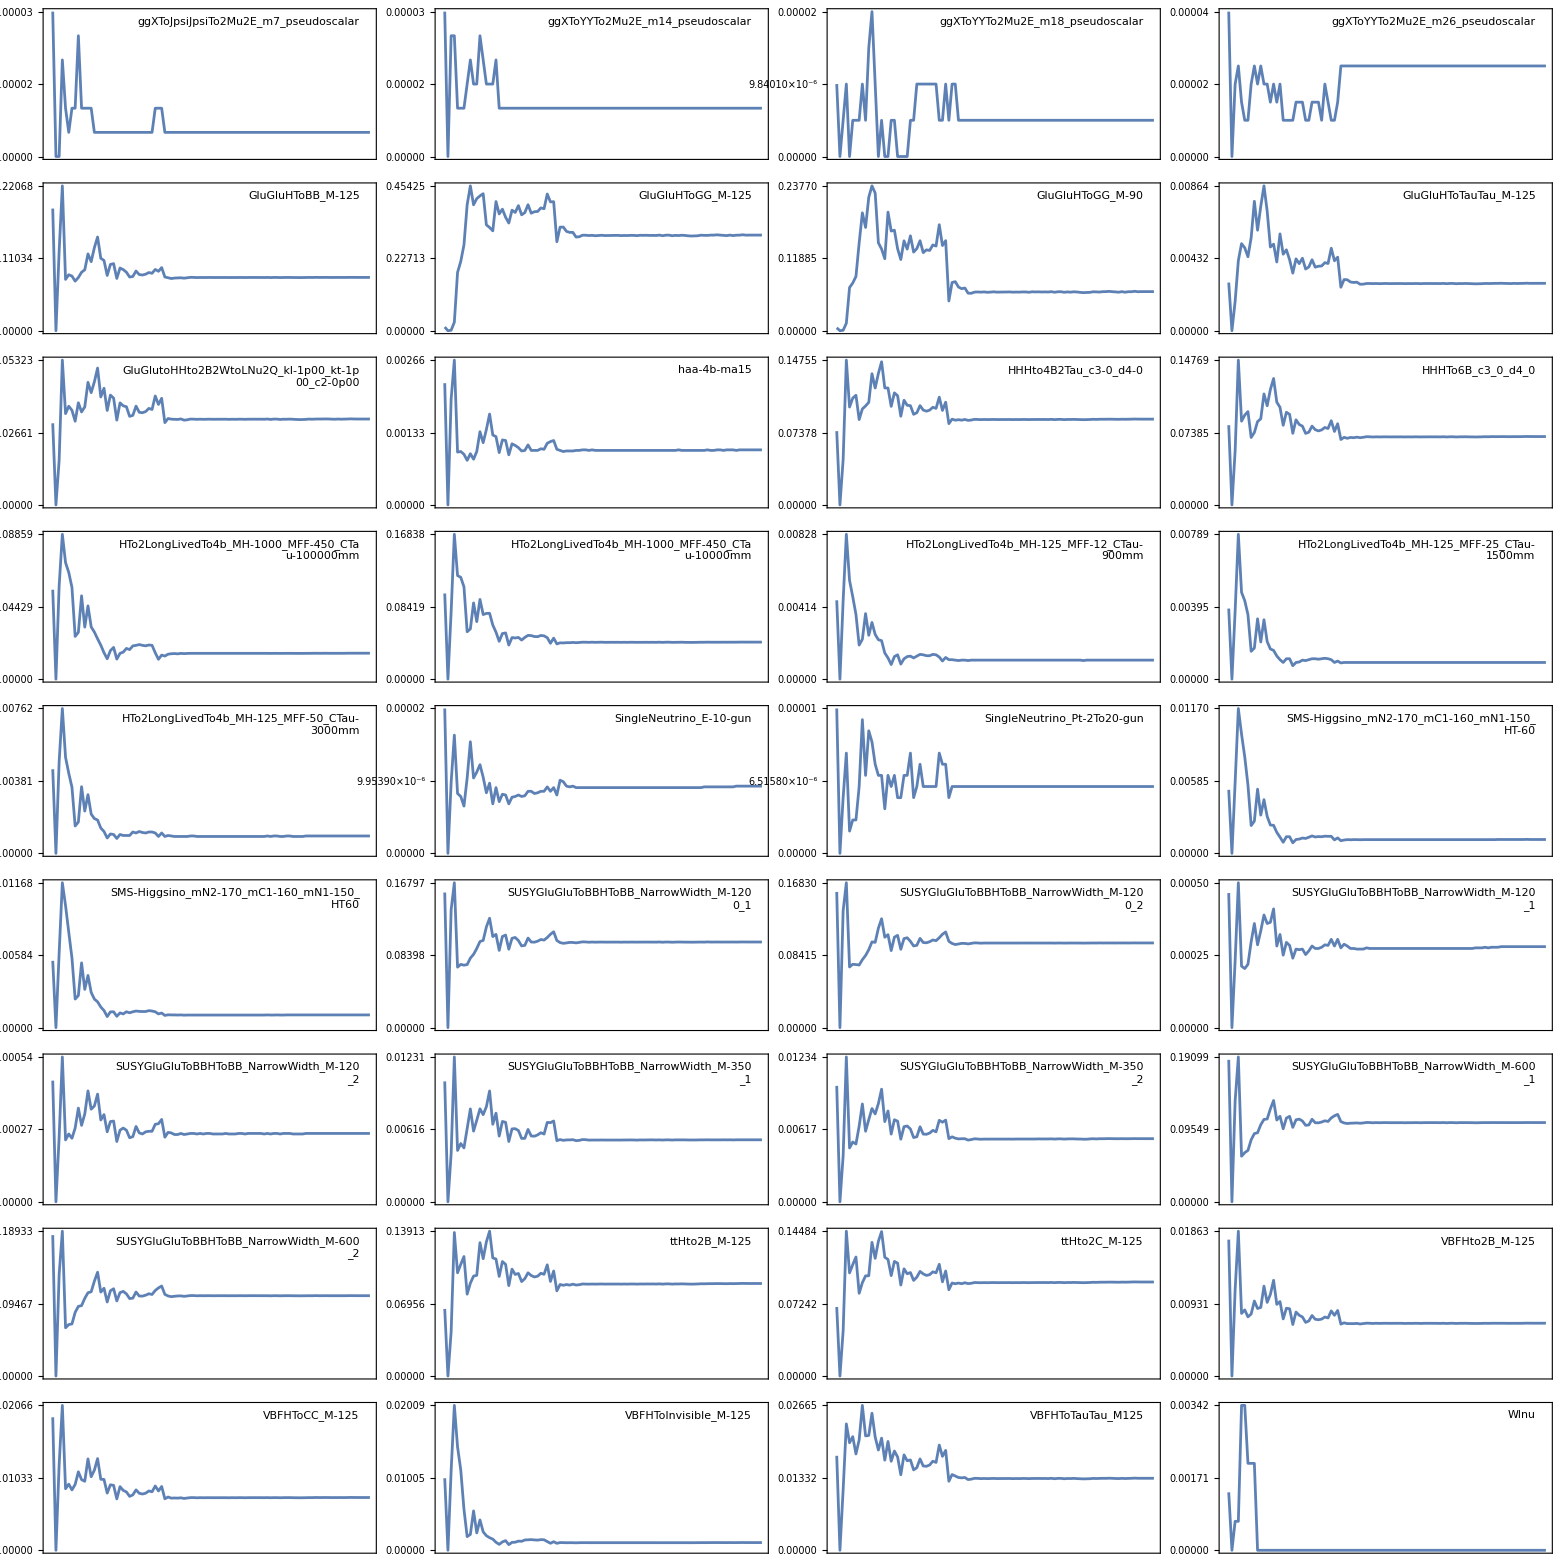
TPR @ 10^-5 FPR (probs.) | -Graphics-
 | Epochs ∈ [0, 100]

```mathematica
selectedRunPlotData = plotData[selectedRun];
makePlot[row_,label_]:=ListLinePlot[
row,
PlotStyle->{Medium},
Axes->False,
Frame->True,
FrameTicks->
{
{
{
{Min[row],NumberForm[N[Min[row]],{5,5}]},
{(Min[row]+(Max[row] - Min[row])/2),NumberForm[N[Min[row]+(Max[row] - Min[row])/2],{5,5}]},
{Max[row],NumberForm[N[Max[row]],{5,5}]}},None
},
{None,None}
},
FrameTicksStyle->Directive[11,FontWeight->"Plain"],
PlotRange->{All, {Min[row], Max[row]}},
ImageSize->300,
PlotLabel->None,
Epilog->{Inset[Style[label,11,FontWeight->"Plain",Background->White],Scaled[{0.95,0.95}],{Right,Top}]}
]
datasetNamesWrapped=wrapLabel[#,37]&/@datasetNames;
plots=MapThread[makePlot,{selectedRunPlotData,datasetNamesWrapped}];

possiblePartitions = Divisors[Length@datasetNames];
plotsPerRow = possiblePartitions[[4]];
grid=Partition[plots,4];

fullGridWithAxes=Grid[{{"",Grid[grid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24, Gray]}},Spacings->{1,2}];
Row[{Style[Rotate[desiredMetricPlotStyling[desiredMetric],90 Degree],FontWeight->"SemiBold",24, Gray],Spacer[10],fullGridWithAxes}]
```

```mathematica
Export["dataset_grids/" <>FileBaseName@desiredMetric <> "_" <>desiredRun <> ".png",%]
```

StringJoin::string: String expected at position 2 in dataset_grids/kl_<>desiredRun<>.png.

Export::chtype: First argument dataset_grids/kl_<>desiredRun<>.png is not a valid file specification.

$Failed

# Overall Plot

```mathematica
datasetPlotStyling=<|
"train"->"Zero Bias Train",
"ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar"->"gg → X_(7 GeV) → J/ψ J/ψ → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m14_pseudoscalar"->"gg → X_(14 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m18_pseudoscalar"->"gg → X_(18 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m26_pseudoscalar"->"gg → X_(26 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"GluGluHToBB_M-125"-> "gg → H(125 GeV) → bb̄",
"GluGluHToGG_M-125"-> "gg → H(125 GeV) → gg",
"GluGluHToGG_M-90"->"gg → H(90 GeV) → gg", 
"GluGluHToTauTau_M-125"-> "gg → H(125 GeV) → τ^+τ^-",
"GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00"-> "gg → HH → bb̄W^+W^- → (l^±ν)(qq̄')",
"HHHto4B2Tau_c3-0_d4-0" -> "HHH → bb̄bb̄τ^+τ^-",
"HHHTo6B_c3_0_d4_0"->"HHH → 6b",
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm"-> "H (10^3 GeV) → LL (10^3 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm" -> "H (125 GeV) → LL (900 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm" ->"H (125 GeV) → LL (1500 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm" -> "H (125 GeV) → LL (3000 mm) → 4b",
"haa-4b-ma15"->"H → AA → 4b", 
"VBFHto2B_M-125"->"VV → H → bb̄", 
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm" -> "H (10^3 GeV) → 2LL (10^4 mm) → 4b", 
"main_val"->"Zero Bias Validation",
"SingleNeutrino_E-10-gun" -> "Zero Bias Simulation",
"SingleNeutrino_Pt-2To20-gun" -> "Zero Bias Simulation",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60" -> "higgsino",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60" ->"higgsino",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_1" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_2" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_1" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_2" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_1" -> "gg → bb̄H(600 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_2"-> "gg → bb̄H(600 GeV) → bb̄",
"ttHto2B_M-125" -> "tt̄ → H(125 GeV) → bb̄",
"ttHto2C_M-125" -> "tt̄ → H(125 GeV) → cc̄",
"VBFHToCC_M-125"->"VV → H → cc̄",
"VBFHToInvisible_M-125"->"VV → H → invis",
"VBFHToTauTau_M125"->"VV → H → τ^+τ^-",
"Wlnu" -> "W^± → l^±ν_l",
"WToTauTo3Mu" -> "W^± → τ^± → μ^±μ^+μ^-",
"WToTauToMuMuMu" -> "W^± → τ^± → μ^±μ^+μ^-"
|>;
labels = Style[#,FontSize->22, Italic]&/@(datasetPlotStyling/@datasetNames);

ClearAll[processRunName];
processRunName[runName_]:=Module[{datasetKey},
datasetKey=(Flatten@StringSplit[runName,"_",3])[[3]];
If[KeyExistsQ[datasetPlotStyling,datasetKey],datasetPlotStyling[datasetKey]]
]


(*Color function for selected lines*)
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
colorFunc=Function[i,RGBColor[hexColors[[Mod[i-1,Length[hexColors]]+1]]]];

(*Get Unique Simulations*)
duplicateLabels = Select[PositionIndex[labels], Length[#] > 1 &];
dupPositionsIgnoringFirst=Select[duplicateLabels,Length[#]>1&]  //Values //Map[Rest] //Flatten;
uniqueLabels = DeleteDuplicates[labels];
plotDataSingle = Map[Delete[#,List/@dupPositionsIgnoringFirst]&,plotData];

(*Restart:compute and plot max-index for each row of each dataset in plotData*)(*1. Build an association mapping each key to a list of {columnIndexOfMax,rowIndex}*)
xyPlotData=KeyValueMap[Function[{key,mat},key->Table[{Max[mat[[i]]],i},{i,Length@mat}]],plotDataSingle];

(*2. Extract only the value lists for plotting,but keep keys for legend*)
series=Values@xyPlotData;
labelsKeysRaw=Keys@xyPlotData;
labelsKeys = Style[#,FontSize->22, Italic]&/@Flatten[processRunName/@labelsKeysRaw];
yTicks=Table[{i,uniqueLabels[[i]]},{i,Length@uniqueLabels}];
yTicksRight=yTicks/. {v_,_}:>{v,""};


(*3. Scale x-axis values and compute ticks*)
allXValues=Flatten[series[[All,All,1]]];
scaleExp=Floor[Log10[Max[Abs[allXValues]]]];
scaleFactor=10^scaleExp;
scaledSeries=Map[{#[[1]]/scaleFactor,#[[2]]}&,series,{2}];

(*Tick lengths*)
majorLen=Scaled[0.02];
minorLen=Scaled[0.01];
minX=Min@scaledSeries[[All,All,1]];
maxX=Max@scaledSeries[[All,All,1]];
step=(maxX-minX)/5;

majors=Table[{x,Style[NumberForm[x,{2,2}],Black,FontSize->24,FontFamily->"TeX Gyre Heros"],{majorLen,0}},{x,minX,maxX,step}];
(*Five minor ticks between each pair of major ticks:subdivide each major interval into 6 parts*)
minors=Flatten[Table[Table[{x0+i*(step/6),"",{minorLen,0}},{i,1,5}],{x0,minX,maxX,step}],1];

bottomTicks=Join[majors, minors];
(*bottomTicks=majors;*)
upperTicks=bottomTicks/. {v_,_,len_}:>{v,"",len};

xGrid=bottomTicks[[All,1]];
yGrid=yTicks[[All,1]];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText = Row[{Style["14 TeV",FontFamily->"TeX Gyre Heros",24],""}];

plt = ListLinePlot[
scaledSeries,
PlotMarkers->Table[{Automatic,16},{Length@series}],
GridLines->{xGrid,yGrid},
GridLinesStyle->Directive[GrayLevel[0.5],Dashed],
Joined->True,
Axes->False, 
PlotRange->All, 
PlotStyle->(colorFunc/@Range[Length@series]),
Frame->True,
FrameTicks->{{yTicks,yTicksRight},{bottomTicks,upperTicks}},
FrameLabel->{Style[Row[{ desiredMetricPlotStyling[desiredMetric],If[scaleExp != 0,Row[{" ×",Superscript[10,scaleExp]}],""],""}],Black,FontSize->30,FontFamily->"TeX Gyre Heros"],""},
LabelStyle->Directive[Black,FontSize->28,FontFamily->"TeX Gyre Heros"],
PlotLegends->Placed[LineLegend[labelsKeys, LegendMarkerSize->22, LabelStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"]],Scaled[{0.8,0.93}]],
FrameTicksStyle->Directive[AbsoluteThickness[2]],
Epilog->{},
PlotRangePadding->{{0.1,0.1},{Scaled[0.01],Scaled[0.02]}},
ImageSize->1300,
AspectRatio->1.5
];

outer=Graphics[{Inset[plt,Scaled[{0,0}],{Left,Bottom},Scaled[1]],Inset[cmsText,Scaled[{0.36,0.985}],{Left,Top}, Scaled[1]],Inset[tevText,Scaled[{0.895,0.97}],{Left,Bottom},Scaled[1]]},PlotRange->{{0,1},{0,1}}, AspectRatio->1, ImageSize->1300]
```

-Graphics-

```mathematica
Export["final_presentation_plots/" <>"haa_gghgg_vvHtautau_" <> desiredMetric <>".pdf",outer]
```

final_presentation_plots/haa_gghgg_vvHtautau_score_rate0.3.pdf

```mathematica
Export["final_presentation_plots/" <>"hhh6b_gghgg125_hhh4b2tau_" <> desiredMetric <>".pdf",outer]
```

final_presentation_plots/hhh6b_gghgg125_hhh4b2tau_score_rate0.3.pdf

```mathematica
Export["final_presentation_plots/" <>"hhh6b_tthcc_tthbb_" <> desiredMetric <>".pdf",outer]
```

final_presentation_plots/hhh6b_tthcc_tthbb_score_rate0.3.pdf

# Plot of Supervised TPRs for every data set

```mathematica
(*1) Discover your runs*)
experimentDir=FileNameJoin[{dataDir,experimentName}];
runDirs=FileNames[All,experimentDir];
runNames=FileNameTake/@runDirs;

(*2) Build the association for every runName*)
pathsByRun=Association@Table[runName->Module[{runDir,files},(*find the directory matching this runName*)
runDir=SelectFirst[runDirs,StringContainsQ[#,runName]&];
(*grab all files in that directory*)
files=FileNames[All,runDir];
(*filter by metric and drop “test” files*)
files=Select[files,StringContainsQ[#,desiredMetric<>"."]&];
files=Select[files,StringFreeQ[#,"test"]&];
(*if it’s a “rate” metric drop the main_ files too*)
If[StringContainsQ[desiredMetric,"rate"],DeleteCases[files,_?(StringContainsQ[#,"main_"]&)],files]],{runName,runNames}];

(*3) (Optional) print out counts per run*)
Column@Prepend[KeyValueMap[(#1<>": "<>ToString[Length[#2]]<>" files")&,pathsByRun],Style["Files per run:",Bold]]
```

Files per run:
scan_lr0.001_ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar: 38 files
scan_lr0.001_ggXToYYTo2Mu2E_m14_pseudoscalar: 38 files
scan_lr0.001_ggXToYYTo2Mu2E_m18_pseudoscalar: 38 files
scan_lr0.001_ggXToYYTo2Mu2E_m26_pseudoscalar: 38 files
scan_lr0.001_GluGluHToBB_M-125: 38 files
scan_lr0.001_GluGluHToGG_M-125: 38 files
scan_lr0.001_GluGluHToGG_M-90: 38 files
scan_lr0.001_GluGluHToTauTau_M-125: 38 files
scan_lr0.001_GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00: 38 files
scan_lr0.001_haa-4b-ma15: 38 files
scan_lr0.001_HHHto4B2Tau_c3-0_d4-0: 38 files
scan_lr0.001_HHHTo6B_c3_0_d4_0: 38 files
scan_lr0.001_HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm: 38 files
scan_lr0.001_HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm: 38 files
scan_lr0.001_HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm: 38 files
scan_lr0.001_HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm: 38 files
scan_lr0.001_HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm: 38 files
scan_lr0.001_SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60: 38 files
scan_lr0.001_SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-120_1: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-120_2: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-350_1: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-350_2: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-600_1: 38 files
scan_lr0.001_SUSYGluGluToBBHToBB_NarrowWidth_M-600_2: 38 files
scan_lr0.001_ttHto2B_M-125: 38 files
scan_lr0.001_ttHto2C_M-125: 38 files
scan_lr0.001_VBFHto2B_M-125: 38 files
scan_lr0.001_VBFHToCC_M-125: 38 files
scan_lr0.001_VBFHToInvisible_M-125: 38 files
scan_lr0.001_VBFHToTauTau_M125: 38 files
scan_lr0.001_Wlnu: 38 files
scan_lr0.001_WToTauTo3Mu: 38 files
scan_lr0.001_WToTauToMuMuMu: 38 files

```mathematica
selectedRun = "";
datasetNames = {};
desiredRuns = Keys@pathsByRun;
DynamicModule[{},
Column[{Style["Pick one run:",Bold],
PopupMenu[Dynamic[selectedRun,
(
selectedRun=#;
datasetNames=processDatasetNames/@Lookup[pathsByRun,selectedRun,{}];
)&],
desiredRuns],
Dynamic[If[selectedRun===""||datasetNames==={},"⟨No datasets to display⟩",Framed[Pane[Column[datasetNames],{350,150},Scrollbars->True]]]]
}
]
]
```

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
plotData = Association[Table[runName ->Table[BinaryReadList[pathsByRun[runName][[i]], "Real32"], {i, 1, Length@pathsByRun[runName]}],{runName,Keys[pathsByRun] }]];
plotData[[selectedRun]] //Dimensions
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Map[Clip[#,{0,2}]&, plotData]];
If[desiredMetric == "loss",plotData =Map[Clip[#,{0,4}]&, plotData]];
If[StringContainsQ[desiredMetric, "rate"], plotData = plotData/bcRateKHz];
```

{38,100}

```mathematica
datasetPlotStyling=<|
"train"->"Zero Bias Train",
"ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar"->"gg → X_(7 GeV) → J/ψ J/ψ → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m14_pseudoscalar"->"gg → X_(14 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m18_pseudoscalar"->"gg → X_(18 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m26_pseudoscalar"->"gg → X_(26 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"GluGluHToBB_M-125"-> "gg → H(125 GeV) → bb̄",
"GluGluHToGG_M-125"-> "gg → H(125 GeV) → gg",
"GluGluHToGG_M-90"->"gg → H(90 GeV) → gg", 
"GluGluHToTauTau_M-125"-> "gg → H(125 GeV) → τ^+τ^-",
"GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00"-> "gg → HH → bb̄W^+W^- → (l^±ν)(qq̄')",
"HHHto4B2Tau_c3-0_d4-0" -> "HHH → bb̄bb̄τ^+τ^-",
"HHHTo6B_c3_0_d4_0"->"HHH → 6b",
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm"-> "H (10^3 GeV) → LL (10^3 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm" -> "H (125 GeV) → LL (900 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm" ->"H (125 GeV) → LL (1500 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm" -> "H (125 GeV) → LL (3000 mm) → 4b",
"haa-4b-ma15"->"H → AA → 4b", 
"VBFHto2B_M-125"->"VV → H → bb̄", 
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm" -> "H (10^3 GeV) → 2LL (10^4 mm) → 4b", 
"main_val"->"Zero Bias Validation",
"SingleNeutrino_E-10-gun" -> "Zero Bias Simulation",
"SingleNeutrino_Pt-2To20-gun" -> "Zero Bias Simulation",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60" -> "higgsino",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60" ->"higgsino",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_1" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_2" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_1" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_2" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_1" -> "gg → bb̄H(600 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_2"-> "gg → bb̄H(600 GeV) → bb̄",
"ttHto2B_M-125" -> "tt̄ → H(125 GeV) → bb̄",
"ttHto2C_M-125" -> "tt̄ → H(125 GeV) → cc̄",
"VBFHToCC_M-125"->"VV → H → cc̄",
"VBFHToInvisible_M-125"->"VV → H → invis",
"VBFHToTauTau_M125"->"VV → H → τ^+τ^-",
"Wlnu" -> "W^± → l^±ν_l",
"WToTauTo3Mu" -> "W^± → τ^± → μ^±μ^+μ^-",
"WToTauToMuMuMu" -> "W^± → τ^± → μ^±μ^+μ^-"
|>;
labels = Style[#,FontSize->22, Italic]&/@(datasetPlotStyling/@datasetNames);

ClearAll[processRunName];
processRunName[runName_]:=Module[{datasetKey},
datasetKey=(Flatten@StringSplit[runName,"_",3])[[3]];
If[KeyExistsQ[datasetPlotStyling,datasetKey],datasetPlotStyling[datasetKey]]
]


(*Color function for selected lines*)
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
colorFunc=Function[i,RGBColor[hexColors[[Mod[i-1,Length[hexColors]]+1]]]];

(*Get Unique Simulations*)
duplicateLabels = Select[PositionIndex[labels], Length[#] > 1 &];
dupPositionsIgnoringFirst=Select[duplicateLabels,Length[#]>1&]  //Values //Map[Rest] //Flatten;
uniqueLabels = DeleteDuplicates[labels];
plotDataSingle = Map[Delete[#,List/@dupPositionsIgnoringFirst]&,plotData];

(*Restart:compute and plot max-index for each row of each dataset in plotData*)(*1. Build an association mapping each key to a list of {columnIndexOfMax,rowIndex}*)
xyPlotData=KeyValueMap[Function[{key,mat},key->Table[{Max[mat[[i]]],i},{i,Length@mat}]],plotDataSingle];

(*2. Extract only the value lists for plotting,but keep keys for legend*)

labelsKeysRaw=Keys@xyPlotData;

consideredDatasets = (Flatten@StringSplit[#,"_",3])[[3]] &/@ labelsKeysRaw ;
consideredDatasets = DeleteDuplicatesBy[consideredDatasets,datasetPlotStyling];
consideredDatasets = Style[#,FontSize->22, Italic]&/@(datasetPlotStyling/@consideredDatasets);
consideredDatasetsIdx = Flatten[(Flatten@Position[uniqueLabels,#])&/@consideredDatasets];
consideredDatasetsTPR = Table[{Lookup[xyPlotData, labelsKeysRaw[[i]]][[consideredDatasetsIdx[[i]]]][[1]], i},{i, Length@consideredDatasets}];
series = {consideredDatasetsTPR};

labelsKeys = consideredDatasets;
yTicks=Table[{i,consideredDatasets[[i]]},{i,Length@consideredDatasets}];
yTicksRight=yTicks/. {v_,_}:>{v,""};

(*3. Scale x-axis values and compute ticks*)
allXValues=Flatten[series[[All,All,1]]];
scaleExp=Floor[Log10[Max[Abs[allXValues]]]];
scaleFactor=10^scaleExp;
scaledSeries=Map[{#[[1]]/scaleFactor,#[[2]]}&,series,{2}];

(*Tick lengths*)
majorLen=Scaled[0.02];
minorLen=Scaled[0.01];
minX=Min@scaledSeries[[All,All,1]];
maxX=Max@scaledSeries[[All,All,1]];
step=(maxX-minX)/5;

majors=Table[{x,Style[NumberForm[x,{2,2}],Black,FontSize->24,FontFamily->"TeX Gyre Heros"],{majorLen,0}},{x,minX,maxX,step}];
(*Five minor ticks between each pair of major ticks:subdivide each major interval into 6 parts*)
minors=Flatten[Table[Table[{x0+i*(step/6),"",{minorLen,0}},{i,1,5}],{x0,minX,maxX,step}],1];

bottomTicks=Join[majors, minors];
(*bottomTicks=majors;*)
upperTicks=bottomTicks/. {v_,_,len_}:>{v,"",len};

xGrid=bottomTicks[[All,1]];
yGrid=yTicks[[All,1]];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText = Row[{Style["14 TeV",FontFamily->"TeX Gyre Heros",24],""}];

plt = ListLinePlot[
scaledSeries,
PlotMarkers->Table[{Automatic,16},{Length@series}],
GridLines->{xGrid,yGrid},
GridLinesStyle->Directive[GrayLevel[0.5],Dashed],
Joined->True,
Axes->False, 
PlotRange->All, 
PlotStyle->(colorFunc/@Range[Length@series]),
Frame->True,
FrameTicks->{{yTicks,yTicksRight},{bottomTicks,upperTicks}},
FrameLabel->{Style[Row[{ desiredMetricPlotStyling[desiredMetric],If[scaleExp != 0,Row[{" ×",Superscript[10,scaleExp]}],""],""}],Black,FontSize->30,FontFamily->"TeX Gyre Heros"],""},
LabelStyle->Directive[Black,FontSize->28,FontFamily->"TeX Gyre Heros"],
(*PlotLegends->Placed[SwatchLegend[labelsKeys, LegendMarkerSize->15, LabelStyle->Directive[Black,FontSize->20,FontFamily->"TeX Gyre Heros"]],Scaled[{0.73,0.97}]],*)
FrameTicksStyle->Directive[AbsoluteThickness[2]],
Epilog->{},
PlotRangePadding->{{0.15,0.15},{Scaled[0.01],Scaled[0.02]}},
ImageSize->1300,
AspectRatio->1.5
];

outer=Graphics[{Inset[plt,Scaled[{0,0}],{Left,Bottom},Scaled[1]],Inset[cmsText,Scaled[{0.36,0.985}],{Left,Top}, Scaled[1]],Inset[tevText,Scaled[{0.895,0.97}],{Left,Bottom},Scaled[1]]},PlotRange->{{0,1},{0,1}}, AspectRatio->1, ImageSize->1300]
```

-Graphics-

```mathematica
Export["final_presentation_plots/" <>"supervised_TPRs_lr0.001.pdf",outer]
```

final_presentation_plots/supervised_TPRs_lr0.001.pdf